# Chebyshev interpolation: from the flux grid to an interpolant

This notebook builds, step by step, the interpolant in FluxInterpolation.wl from the numbers produced by FluxGrid_nonspinning.nb. Evaluate the cells in order. Exercises are marked; their solutions are in closed cell groups (click the bracket on the right to open them). Try them first.

Roadmap: (1) why not a plain polynomial fit on equally spaced points, (2) Chebyshev polynomials, (3) Chebyshev nodes, (4) 1D interpolation and its coefficients, (5) error and convergence, (6) 2D tensor-product interpolation, (7) the real flux data and the map to physical variables.

```mathematica
dir = If[$FrontEnd === Null, "/home/luca/repos/hyb_env_model/Mathematica", NotebookDirectory[]];
```

## 1. The problem: interpolating with polynomials

We know a smooth function f only at n points and want it everywhere in between, cheaply and accurately. The obvious choice is the unique polynomial of degree n-1 through the n points. Whether this works depends almost entirely on where the points are.

Classic example (Runge): f(x) = 1/(1+25x^2) on [-1,1]. Below, the interpolating polynomial through 15 equally spaced points (red) versus 15 Chebyshev points (blue).

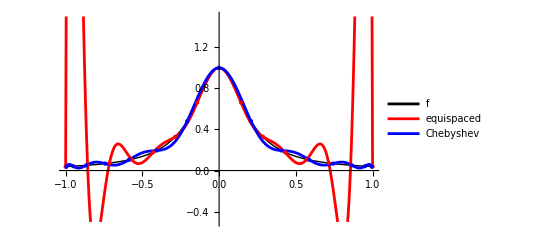

```mathematica
runge[x_] := 1/(1 + 25 x^2);
n = 15;
xsEq = Subdivide[-1., 1., n - 1];
xsCh = Table[Cos[(2 i + 1) Pi/(2 n)], {i, 0, n - 1}] // N;
pEq[x_] = InterpolatingPolynomial[Transpose[{xsEq, runge /@ xsEq}], x];
pCh[x_] = InterpolatingPolynomial[Transpose[{xsCh, runge /@ xsCh}], x];
Plot[{runge[x], pEq[x], pCh[x]}, {x, -1, 1}, PlotRange -> {-0.5, 1.5},
 PlotStyle -> {Directive[Black, Thick], Red, Blue},
 PlotLegends -> {"f", "equispaced", "Chebyshev"},
 Epilog -> {Red, PointSize[Medium], Point[Transpose[{xsEq, runge /@ xsEq}]], Blue, Point[Transpose[{xsCh, runge /@ xsCh}]]}]
```

The equispaced polynomial oscillates wildly near the edges, and it gets worse as n grows. The Chebyshev one converges. The Chebyshev points cluster near the endpoints, like the projection onto the x axis of equally spaced points on a semicircle. That clustering is the whole trick.

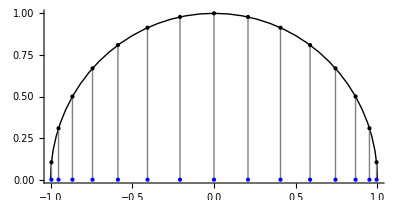

```mathematica
Graphics[{Circle[{0, 0}, 1, {0, Pi}], Table[{Gray, Line[{{Cos[t], Sin[t]}, {Cos[t], 0}}], Blue, PointSize[Medium], Point[{Cos[t], 0}], Black, Point[{Cos[t], Sin[t]}]}, {t, Table[(2 i + 1) Pi/(2 n), {i, 0, n - 1}]}]}, Axes -> {True, False}]
```

## 2. Chebyshev polynomials

For x in [-1,1] write x = cos θ. The Chebyshev polynomial of degree k is defined by

T_k(cos(θ))==cos(k θ)

i.e. T_k(x) = cos(k arccos x). Using cos((k+1)θ) + cos((k-1)θ) = 2 cos θ cos kθ gives the three-term recurrence, which shows that T_k really is a polynomial:

T_0(x)==1

T_1(x)==x

T_(k+1)(x)==2 x T_k(x)-T_(k-1)(x)

Key properties:

|T_k(x)| ≤ 1 on [-1,1], and T_k oscillates between ±1 exactly k+1 times. So a coefficient c_k multiplying T_k contributes at most |c_k| anywhere in the interval. This is why the size of the coefficients directly measures the size of each term.

T_k has k roots in [-1,1], all real.

They are orthogonal with weight 1/√(1-x.b2). We will need the discrete version (Section 3).

Mathematica has them built in as ChebyshevT:

```mathematica
Table[ChebyshevT[k, x], {k, 0, 5}] // TableForm
```

1
x
-1+2 x^2
-3 x+4 x^3
1-8 x^2+8 x^4
5 x-20 x^3+16 x^5

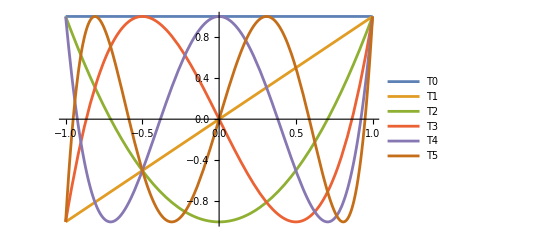

```mathematica
Plot[Evaluate@Table[ChebyshevT[k, x], {k, 0, 5}], {x, -1, 1}, PlotLegends -> Table["T" <> ToString[k], {k, 0, 5}]]
```

For numerics we never expand them in powers of x. We evaluate all of T_0 … T_{n-1} at once from the cosine definition. This is the function used in the package:

```mathematica
chebT[n_, x_] := Cos[Range[0, n - 1] ArcCos[x]];
chebT[6, 0.3]
ChebyshevT[Range[0, 5], 0.3]
```

{1.,0.3,-0.82,-0.792,0.3448,0.99888}

{1.,0.3,-0.82,-0.792,0.3448,0.99888}

### Exercise 1

(a) Check the recurrence symbolically for k = 1, …, 8 using ChebyshevT. (b) Check that chebT[n, x] agrees with ChebyshevT for a few random x in [-1,1]. (c) What does chebT return for x = 1.5, and why? (Hint: ArcCos of a number > 1.)

```mathematica
RecurrCheck[k_]:=ChebyshevT[k+1,x]-(2 x ChebyshevT[k,x]-ChebyshevT[k-1,x])
Polys=Table[RecurrCheck[k]//Simplify, {k, 1, 8}]//TableForm
```

0
0
0
0
0
0
0
0

```mathematica
chebT[6,1.5]
```

{1.+0. ⅈ,1.5+0. ⅈ,3.5+0. ⅈ,9.+0. ⅈ,23.5+0. ⅈ,61.5+0. ⅈ}

#### Solution

```mathematica
Table[Expand[ChebyshevT[k + 1, x] - (2 x ChebyshevT[k, x] - ChebyshevT[k - 1, x])], {k, 1, 8}]
```

```mathematica
Max@Table[With[{x = RandomReal[{-1, 1}]}, Max@Abs[chebT[10, x] - ChebyshevT[Range[0, 9], x]]], {20}]
```

```mathematica
chebT[4, 1.5]
```

ArcCos[1.5] is complex, so chebT returns complex numbers with tiny imaginary parts; the real parts are still T_k(1.5) (= cosh(k arccosh 1.5)), but the cosine formula is only meant for |x| ≤ 1. Chebyshev interpolants are defined on [-1,1]; outside it they grow like the T_k themselves (exponentially in k), so extrapolation is meaningless. The package therefore refuses to evaluate outside the square.

## 3. Chebyshev–Gauss nodes and discrete orthogonality

The interpolation points are the n roots of T_n: cos(nθ) = 0 gives θ_i = (2i+1)π/(2n), so

x_i==cos(((2 i+1) π)/(2 n))

with i = 0, …, n-1. These are the Chebyshev–Gauss (or "first kind") nodes. This is exactly the function node[i, n] in FluxGrid_nonspinning.nb:

```mathematica
node[i_, n_] := Cos[(2 i + 1) Pi/(2 n)];
Table[node[i, 6], {i, 0, 5}] // N
```

{0.965926,0.707107,0.258819,-0.258819,-0.707107,-0.965926}

Note the ordering: i = 0 is the point closest to +1 and i = n-1 the point closest to -1. In the flux grid, row i = 0 is rC ≈ +1 (the ISCO) and column j = 0 is χ ≈ +1 (prograde).

The property that makes everything work is discrete orthogonality. For 0 ≤ k, l ≤ n-1:

∑_(i=0)^(n-1) T_k(x_i) T_l(x_i)==(Piecewise[{{0, k≠l}, {n, k==l==0}, {n/2, k==l≠0}}])

It follows from T_k(x_i) = cos(kθ_i) and the sum of cosines of equally spaced angles. Numerically:

```mathematica
With[{n = 6}, Table[Sum[ChebyshevT[k, node[i, n]] ChebyshevT[l, node[i, n]], {i, 0, n - 1}], {k, 0, n - 1}, {l, 0, n - 1}] // N // Chop // MatrixForm]
```

(6. | 0 | 0 | 0 | 0 | 0
0 | 3. | 0 | 0 | 0 | 0
0 | 0 | 3. | 0 | 0 | 0
0 | 0 | 0 | 3. | 0 | 0
0 | 0 | 0 | 0 | 3. | 0
0 | 0 | 0 | 0 | 0 | 3.)

### Exercise 2

(a) Verify that node[i, n] are the roots of ChebyshevT[n, x] for n = 7 (use NSolve or evaluate ChebyshevT at the nodes). (b) Repeat the orthogonality check with equally spaced points instead of Chebyshev nodes. Is the matrix still diagonal?

```mathematica
NSolve[ChebyshevT[7,x]==0]
Table[node[i,7],{i,0,6}]//N
```

{{x→-0.974928},{x→-0.781831},{x→-0.433884},{x→0.},{x→0.433884},{x→0.781831},{x→0.974928}}

{0.974928,0.781831,0.433884,0.,-0.433884,-0.781831,-0.974928}

```mathematica
With[{n = 6}, Table[Sum[ChebyshevT[k,x] ChebyshevT[l,x], {x, -1,1,100 }], {k, 0, n - 1}, {l, 0, n - 1}] // N // Chop // MatrixForm]
```

(1. | -1. | 1. | -1. | 1. | -1.
-1. | 1. | -1. | 1. | -1. | 1.
1. | -1. | 1. | -1. | 1. | -1.
-1. | 1. | -1. | 1. | -1. | 1.
1. | -1. | 1. | -1. | 1. | -1.
-1. | 1. | -1. | 1. | -1. | 1.)

#### Solution

```mathematica
Table[ChebyshevT[7, node[i, 7]], {i, 0, 6}] // N // Chop
```

{0,0,0,0,0,0,0}

```mathematica
With[{n = 6, xs = Subdivide[-1., 1., 5]}, Table[Sum[ChebyshevT[k, x] ChebyshevT[l, x], {x, xs}], {k, 0, n - 1}, {l, 0, n - 1}] // Chop // MatrixForm]
```

(6. | 0 | -0.4 | 0 | 1.6992 | 0
0 | 2.8 | 0 | 0.6496 | 0 | 2.24704
-0.4 | 0 | 3.8496 | 0 | 1.19744 | 0
0 | 0.6496 | 0 | 4.39744 | 0 | 1.18192
1.6992 | 0 | 1.19744 | 0 | 4.38192 | 0
0 | 2.24704 | 0 | 1.18192 | 0 | 3.43996)

Not diagonal: the orthogonality is a special property of these nodes.

## 4. 1D interpolation: computing the coefficients

We look for the polynomial of degree n-1 written in the Chebyshev basis

p(x)==∑_(k=0)^(n-1) c_k T_k(x)

with p(x_i) = f_i at the n nodes. Multiply p(x_i) = f_i by T_l(x_i), sum over i, and use discrete orthogonality: every term with k ≠ l drops out and

c_k==(2-k,0)/n ∑_(i=0)^(n-1) f_i cos((k (2 i+1) π)/(2 n))

(The condition /; -1 <= x <= 1 makes chebEval1D return unevaluated outside the interval, see Exercise 1c.)

No linear system to solve: each coefficient is a weighted sum of the data. The (2-δ_{k0}) accounts for the n versus n/2 normalisation. This sum is a discrete cosine transform (type II), so it can be computed with FFT speed if needed.

Since the polynomial of degree n-1 through n points is unique, this is the same polynomial InterpolatingPolynomial would give. We just write it in a better basis: the Chebyshev coefficients are well conditioned and tell us how accurate the result is.

In matrix form c = M · f, with M_{ki} = (2-δ_{k0})/n cos(k(2i+1)π/(2n)):

```mathematica
chebMatrix[n_] := Table[(2 - KroneckerDelta[k, 0])/n Cos[k (2 i + 1) Pi/(2 n)], {k, 0, n - 1}, {i, 0, n - 1}];
chebCoeffs1D[f_List] := N[chebMatrix[Length[f]]] . f; (* dot operator -> a.b = Dot[a,b]. f the list of f_i*)
chebEval1D[c_List, x_?NumericQ] /; -1 <= x <= 1 := chebT[Length[c], x] . c;
```

Example: interpolate g(x) = e^x sin(5x) from 12 nodes.

```mathematica
g[x_] := Exp[x] Sin[5 x];
n = 12;
xs = Table[node[i, n], {i, 0, n - 1}] // N;
cg = chebCoeffs1D[g /@ xs]
```

{-0.386303,-1.01802,-0.785816,-0.94394,-0.13427,0.545923,0.21873,-0.0647728,-0.0427292,0.000803283,0.00361384,0.000362767}

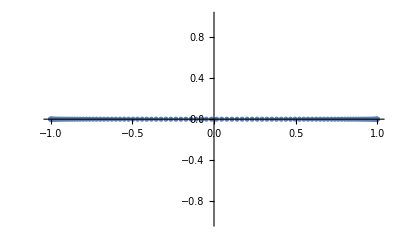

```mathematica
ys[m_] := Table[node[i, m], {i, 0, m - 1}] ;
ListPlot[Transpose[{ys[100],0*ys[100]}]]
```

It reproduces the data at the nodes and approximates g in between:

```mathematica
Max@Abs[(chebEval1D[cg, #] & /@ xs) - (g /@ xs)]
```

8.88178×10^-16

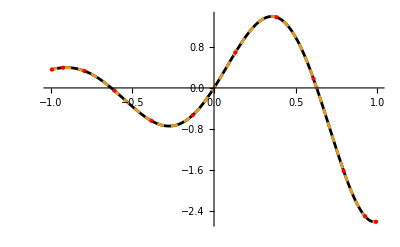

```mathematica
Plot[
{g[x], chebEval1D[cg, x]}, 
{x, -1, 1}, 
PlotStyle -> {Black, Dashed}, 
Epilog -> {
Red, 
PointSize[Medium], 
Point[Transpose[{xs, g /@ xs}]]
}
]
```

### Let me try to reproduce the result but making it human fucking readable

```mathematica
Clear[chebMatrix,chebCoeffs1D,chebEval1D,g,n,xs,cg]
```

```mathematica
chebMatrix[n_] := Table[(2 - KroneckerDelta[k, 0])/n Cos[k((2 i + 1) π)/(2 n)], {k, 0, n - 1}, {i, 0, n - 1}];
chebCoeffs1D[f_List] :=Dot[ N[chebMatrix[Length[f]]] , f];  (* Dot product is the sum over i in the formula for c_k *)
chebEval1D[c_List, x_?NumericQ] /; -1 <= x <= 1 := Dot[chebT[Length[c], x] ,c]; (*Dot product is the sum over k in the formula for the polynomial p(x)*)
```

```mathematica
g[x_] := Exp[x] Sin[5 x];
n = 12;
xs = Table[node[i, n], {i, 0, n - 1}] // N;
cg = chebCoeffs1D[g[xs]] (* g /@ xs is more precise because it works also for non-iterable functions g[x]. But simple mathematical expressions are iterable, so the two are equivalent here*)
```

{-0.386303,-1.01802,-0.785816,-0.94394,-0.13427,0.545923,0.21873,-0.0647728,-0.0427292,0.000803283,0.00361384,0.000362767}

It reproduces the data at the nodes and approximates g in between:

```mathematica
Max@Abs[(Table[chebEval1D[cg, i],{i,xs}]) - (g[xs])]
```

8.88178×10^-16

```mathematica
Plot[
{g[x], chebEval1D[cg, x]}, 
{x, -1, 1}, 
PlotStyle -> {Black, Dashed}, 
Epilog -> {
Red, 
PointSize[Medium], 
Point[Transpose[{xs, g [xs]}]](* converts a list of two long lists (2 x n matrix) into a list of n pairs (n x 2 matrix), so effectively a collection of points*)
}
]
```

-Graphics-

```mathematica
{xs, g [xs]}
Transpose[{xs, g [xs]}]
```

{{0.991445,0.92388,0.793353,0.608761,0.382683,0.130526,-0.130526,-0.382683,-0.608761,-0.793353,-0.92388,-0.991445},{-2.61475,-2.50816,-1.6242,0.179458,1.38099,0.69195,-0.532968,-0.642387,-0.053113,0.332308,0.395261,0.359975}}

{{0.991445,-2.61475},{0.92388,-2.50816},{0.793353,-1.6242},{0.608761,0.179458},{0.382683,1.38099},{0.130526,0.69195},{-0.130526,-0.532968},{-0.382683,-0.642387},{-0.608761,-0.053113},{-0.793353,0.332308},{-0.92388,0.395261},{-0.991445,0.359975}}

### Exercise 3

(a) Show that chebEval1D[cg, x] and InterpolatingPolynomial on the same 12 points are the same polynomial (compare them on a fine grid). (b) The coefficients are also given by the built-in FourierDCT[f, 2]. Find the normalisation factor that relates FourierDCT[g /@ xs, 2] to cg. (c) Implement Clenshaw's algorithm, the standard stable way to evaluate a Chebyshev series without computing cosines: b_k = c_k + 2x b_{k+1} - b_{k+2}, going down from k = n-1 to k = 1 with b_n = b_{n+1} = 0; then p(x) = c_0 + x b_1 - b_2.

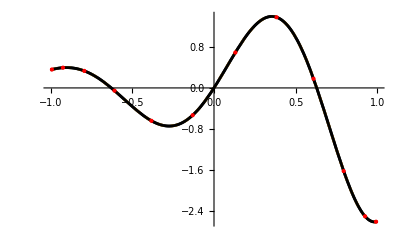

```mathematica
Ip[x_]:=InterpolatingPolynomial[Transpose[{xs,g[xs]}],x]
Plot[
{g[x], chebEval1D[cg, x],Ip[x]} ,
{x, -1, 1}, 
PlotStyle -> {Black, Dashed}, 
Epilog -> {
Red, 
PointSize[Medium], 
Point[Transpose[{xs, g [xs]}]](* converts a list of two long lists (2 x n matrix) into a list of n pairs (n x 2 matrix), so effectively a collection of points*)
}
]
```

```mathematica
Max@Abs[(Table[chebEval1D[cg, x]-Ip[x],{x,-1,1,1000}])]
```

7.21645×10^-16

#### Solution

```mathematica
pLag[x_] = InterpolatingPolynomial[Transpose[{xs, g /@ xs}], x];
Max@Table[Abs[pLag[x] - chebEval1D[cg, x]], {x, -1, 1, 0.01}]
```

2.83107×10^-15

```mathematica
cg/FourierDCT[g /@ xs, 2]
```

So c_k = (2 - δ_{k0})/√n · FourierDCT[f, 2]_k (first entry 1/√12 ≈ 0.289, the others 2/√12 ≈ 0.577).

```mathematica
clenshaw[c_List, x_] := Module[{b1 = 0., b2 = 0., b0},
  Do[b0 = c[[k + 1]] + 2 x b1 - b2; b2 = b1; b1 = b0, {k, Length[c] - 1, 1, -1}];
  c[[1]] + x b1 - b2];
{clenshaw[cg, 0.37], chebEval1D[cg, 0.37], g[0.37]}
```

## 5. Accuracy: convergence and the coefficients as error estimate

How good is the interpolant away from the nodes? Two facts:

Near-best approximation. With Chebyshev nodes the interpolation error is at most (1 + Λ_n) times the error of the best possible polynomial of degree n-1, where the Lebesgue constant Λ_n ~ (2/π) log n grows extremely slowly. For equispaced nodes Λ_n ~ 2^n: that's the Runge disaster.

Convergence rate follows smoothness. For a function analytic in a neighbourhood of [-1,1] the coefficients and the error decay geometrically, like ρ^(-n) ("spectral convergence"). For a function with only k continuous derivatives they decay only algebraically, like n^(-k-1).

Practical consequence: the interpolation error is of the order of the last few coefficients. The truncation error is bounded by the sum of the dropped |c_k|, and aliasing at most doubles it. So we read off the accuracy from the coefficients without knowing the exact function. We use this on the flux grid.

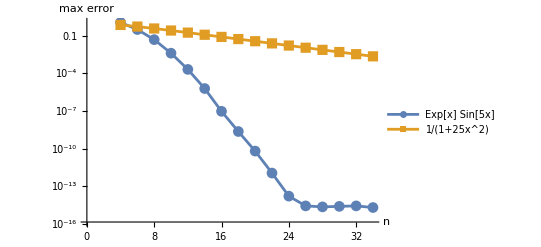

```mathematica
errCheb[f_, n_] := With[
{
c = chebCoeffs1D[f /@ Table[N@node[i, n], {i, 0, n - 1}]]
},
 Max@Table[Abs[f[x] - chebEval1D[c, x]], {x, -1, 1, 0.001}]
];

ListLogPlot[
{
Table[{n, errCheb[g, n]}, {n, 4, 34, 2}],
 Table[{n, errCheb[runge, n]}, {n, 4, 34, 2}]
}, 
Joined -> True,
 PlotMarkers -> Automatic, 
PlotLegends -> {"Exp[x] Sin[5x]", "1/(1+25x^2)"}, 
AxesLabel -> {"n", "max error"}
]
```

Both converge geometrically, until rounding error at ~1e-15. Runge's function converges more slowly because its poles at x = ±i/5 are close to the interval (smaller ρ). Now compare with the coefficients:

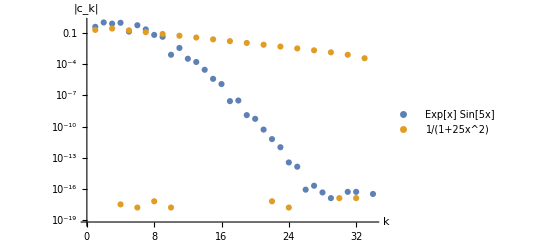

```mathematica
With[{n = 34},
 ListLogPlot[
{
Abs@chebCoeffs1D[g /@ Table[N@node[i, n], {i, 0, n - 1}]],
 Abs@chebCoeffs1D[runge /@ Table[N@node[i, n], {i, 0, n - 1}]]
}, 
PlotLegends -> {"Exp[x] Sin[5x]", "1/(1+25x^2)"},
 AxesLabel -> {"k", "|c_k|"}]
]
```

(The odd coefficients of Runge's function vanish because it is even.)

### Exercise 4

(a) Repeat the convergence plot for |x| and for the step-like tanh(20 x). How do the rates differ, and why? (b) For g with n = 12, compare the actual maximum error with |c_10| + |c_11|. Is "size of the last coefficients" a good estimate?

#### Solution

```mathematica
ListLogLogPlot[{Table[{n, errCheb[Abs, n]}, {n, 4, 64, 4}], Table[{n, errCheb[Tanh[20 #] &, n]}, {n, 4, 64, 4}]}, Joined -> True, PlotMarkers -> Automatic, PlotLegends -> {"|x|", "tanh(20x)"}, AxesLabel -> {"n", "max error"}]
```

|x| has a kink at 0: the error falls only like 1/n (a straight line on the log-log plot). tanh(20x) is analytic but has poles at x = ±iπ/40, very close to the interval, so it converges geometrically only after n is large enough to resolve the steep region. Lesson: Chebyshev interpolation is excellent for smooth functions, and the parametrisation matters. Honet+ change variables (eqs. A11-A12) exactly to make the flux smoother in the new coordinates.

```mathematica
{errCheb[g, 12], Total@Abs@cg[[-2 ;;]]}
```

The estimate is conservative (here about 20 times larger than the true error), which is what you want from an error bar.

## 6. Two dimensions: tensor products

The flux depends on two variables. On a grid of nR × nA Chebyshev nodes (x_i, y_j) with data F_{ij}, use products of 1D polynomials:

p(x,y)==∑_(k=0)^(n_R-1) ∑_(l=0)^(n_A-1) c_(k,l) T_k(x) T_l(y)

Discrete orthogonality holds separately in each direction, so the coefficients factorise: apply the 1D transform to each column (in x), then to each row (in y). With the matrices M_R (nR×nR) and M_A (nA×nA) of Section 4:

C==M_R.F.Transpose[(M_A)]

p(x,y)==Transpose[T(x)].C.T(y)

where T(x) = (T_0(x), …, T_{nR-1}(x)) is what chebT returns. That's the whole package: one matrix product at load time, a vector-matrix-vector product per evaluation.

```mathematica
chebCoeffs2D[F_?MatrixQ] := With[
{
nR = Length[F], 
nA = Length[First[F]]
}, 
N[chebMatrix[nR]] . F . Transpose[N[chebMatrix[nA]]]
];

chebEval2D[cc_?MatrixQ, x_?NumericQ, y_?NumericQ] /; -1 <= x <= 1 && -1 <= y <= 1 := chebT[Length[cc], x] . cc . chebT[Length[First[cc]], y];
```

Test on a toy function on a 10 × 14 grid:

```mathematica
h[x_, y_] := Exp[-x y] Cos[2 x + y];
{nx, ny} = {10, 14};
Fh = Table[h[N@node[i, nx], N@node[j, ny]], {i, 0, nx - 1}, {j, 0, ny - 1}];
Ch = chebCoeffs2D[Fh];
Max@Table[Abs[h[x, y] - chebEval2D[Ch, x, y]], {x, -1, 1, 0.05}, {y, -1, 1, 0.05}]
```

1.21937×10^-6

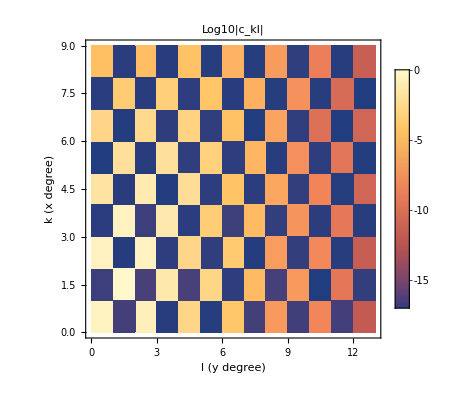

```mathematica
ListDensityPlot[
Log10[Abs[Ch] + 10^-17], 
DataRange -> {{0, ny - 1}, {0, nx - 1}}, 
FrameLabel -> {"l (y degree)", "k (x degree)"}, 
PlotLegends -> Automatic, 
PlotLabel -> "Log10|c_kl|", 
InterpolationOrder -> 0
]
```

The coefficients decay away from the corner (k, l) = (0, 0). The checkerboard is a symmetry: h(-x,-y) = h(x,y), and T_k(-x) = (-1)^k T_k(x), so every c_kl with k + l odd vanishes (dark squares at the 1e-17 floor). The last row and last column of that plot are the error estimate in each direction.

### Exercise 5

(a) Check that chebCoeffs2D[Fh] equals applying chebCoeffs1D first to every column of Fh and then to every row of the result. (b) Increase nx with ny fixed (and vice versa) and watch the error. Which direction limits the accuracy at (10, 14)?

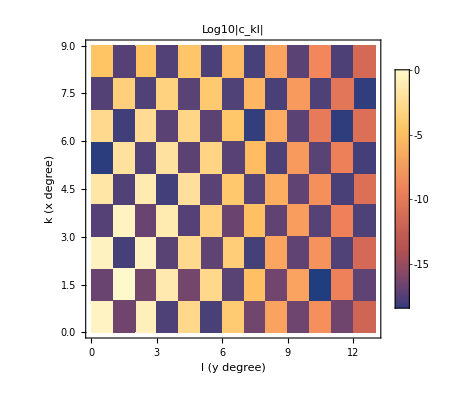

```mathematica
{nx, ny} = {10, 14};
Fh = Table[h[N@node[i, nx], N@node[j, ny]], {i, 0, nx - 1}, {j, 0, ny - 1}];
Ch = chebCoeffs2D[Fh];

ListDensityPlot[
Log10[Abs[Ch] + 10^-30], 
DataRange -> {{0, ny - 1}, {0, nx - 1}}, 
FrameLabel -> {"l (y degree)", "k (x degree)"}, 
PlotLegends -> Automatic, 
PlotLabel -> "Log10|c_kl|", 
InterpolationOrder -> 0
]
```

#### Solution

```mathematica
step1 = Transpose[chebCoeffs1D /@ Transpose[Fh]];
step2 = chebCoeffs1D /@ step1;
Max@Abs[step2 - Ch]
```

```mathematica
err2D[nx_, ny_] := Module[{ff, cc},
  ff = Table[h[N@node[i, nx], N@node[j, ny]], {i, 0, nx - 1}, {j, 0, ny - 1}];
  cc = chebCoeffs2D[ff];
  Max@Table[Abs[h[x, y] - chebEval2D[cc, x, y]], {x, -1, 1, 0.05}, {y, -1, 1, 0.05}]];
{err2D[10, 14], err2D[16, 14], err2D[10, 20]}
```

{1.21937×10^-6,4.50417×10^-13,1.21937×10^-6}

Increasing nx helps much more: x is the limiting direction. You can predict this from the coefficients: compare the size of the last row and the last column of Ch.

```mathematica
{Max@Abs@Ch[[-1]], Max@Abs@Ch[[All, -1]]}
```

{9.55016×10^-6,4.99092×10^-17}

## 7. The real data: the 0PA flux grid

### 7.1 Load and inspect

The grid computed in FluxGrid_nonspinning.nb was saved to data/fluxGrid_nR18_nA27_lmax8.m. It's an nR × nA × 4 array; entry [[i+1, j+1]] = {rC_i, χ_j, r0^5 F_∞, r0^(15/2) F_H} (note the +1: Mathematica lists start at 1, the node index at 0).

```mathematica
data = Get[FileNameJoin[{dir, "data", "fluxGrid_nR18_nA27_lmax8.m"}]];
{nR, nA} = Most@Dimensions[data]
```

{18,27}

Check that the stored coordinates are exactly the Chebyshev nodes, in the expected order:

```mathematica
{Max@Abs[data[[All, 1, 1]] - Table[node[i, nR], {i, 0, nR - 1}]], Max@Abs[data[[1, All, 2]] - Table[node[j, nA], {j, 0, nA - 1}]]} // N
```

{0.,0.}

### 7.2 Why the data are r0^5 F and not F

The coordinates are the compactified ones of Honet+ eq. (A9):

r_C==(2 r_("*"))/r_0-1

χ_C==χ

r_* (χ) is the ISCO radius. r0 = r_* maps to rC = 1, and r0 → ∞ maps to rC = -1: the infinite range of radii fits into [-1,1]. At large r0 the flux behaves like the quadrupole formula, F_∞ ≈ (32/5) r0^(-5), so F_∞ itself is tiny and steep in rC. Factoring out the known leading behaviour (A13, A14),

f_("∞")==r_0^5 F_("∞")

f_("H")==r_0^(15/2) F_("H")

leaves functions of order one that tend to a constant (32/5 for f_∞) at rC = -1. These are much smoother, so need fewer Chebyshev terms. This is the same lesson as in Exercise 4: choose variables that make the function smooth.

```mathematica
Finf = N@data[[All, All, 3]];
Fhor = N@data[[All, All, 4]];
MinMax /@ {Finf, Fhor}
Finf[[-1]] (* row closest to rC = -1, all spins: close to 32/5 = 6.4 *)
```

{{0.252131,8.86837},{-6.4179,28.4592}}

{6.36552,6.37251,6.37712,6.38052,6.38313,6.38521,6.38689,6.38826,6.3894,6.39035,6.39116,6.39184,6.39242,6.39292,6.39335,6.39371,6.39403,6.3943,6.39453,6.39472,6.39488,6.39502,6.39513,6.39522,6.39528,6.39532,6.39534}

### 7.3 One spin first: a 1D interpolation in rC

Fix a column j (one value of χ) and interpolate in rC exactly as in Section 4:

```mathematica
j = 13; (* middle column, χ = 0 *)
{N@node[j, nA], cj = chebCoeffs1D[Finf[[All, j + 1]]]}
```

{0.,{6.42175,0.438393,0.396884,0.0104841,0.0212332,-0.00311635,0.00257583,-0.00112906,0.000691029,-0.000414815,0.000268203,-0.000178571,0.000122102,-0.0000845023,0.0000582842,-0.0000390294,0.0000240207,-0.0000114523}}

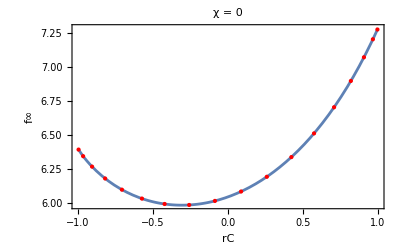

```mathematica
Plot[chebEval1D[cj, rC], {rC, -1, 1}, Epilog -> {Red, PointSize[Medium], Point[Transpose[{data[[All, j + 1, 1]], Finf[[All, j + 1]]}]]}, FrameLabel -> {"rC", "f∞"}, Frame -> True, PlotLabel -> "χ = 0"]
```

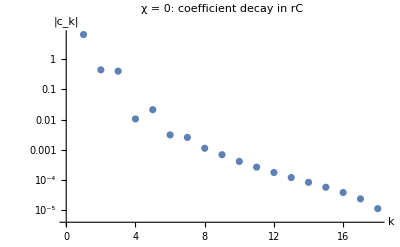

```mathematica
ListLogPlot[Abs[cj], AxesLabel -> {"k", "|c_k|"}, PlotLabel -> "χ = 0: coefficient decay in rC"]
```

### 7.4 Both variables: the full 2D interpolant

```mathematica
Cinf = chebCoeffs2D[Finf];
Chor = chebCoeffs2D[Fhor];
fInfMine[rC_?NumericQ, chi_?NumericQ] := chebEval2D[Cinf, rC, chi];
fHorMine[rC_?NumericQ, chi_?NumericQ] := chebEval2D[Chor, rC, chi];
Max@Table[Abs[fInfMine[data[[i, j, 1]], data[[i, j, 2]]]/Finf[[i, j]] - 1], {i, nR}, {j, nA}]
```

3.44169×10^-15

It reproduces the 486 grid values. Its coefficients are the accuracy diagnostic:

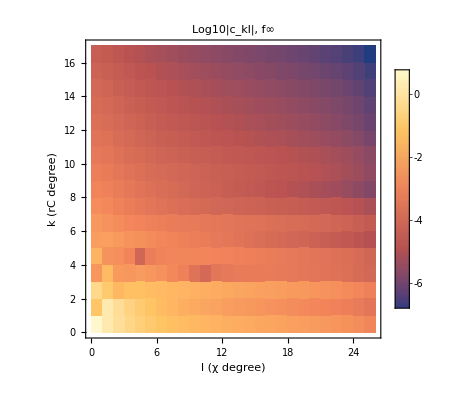

```mathematica
ListDensityPlot[Log10[Abs[Cinf]], DataRange -> {{0, nA - 1}, {0, nR - 1}}, FrameLabel -> {"l (χ degree)", "k (rC degree)"}, PlotLegends -> Automatic, PlotLabel -> "Log10|c_kl|, f∞", InterpolationOrder -> 0]
```

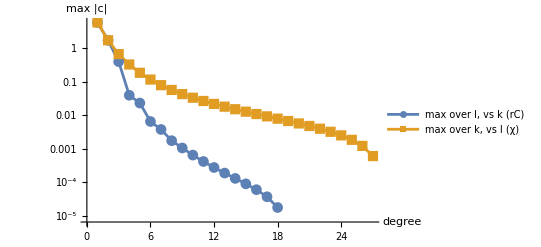

```mathematica
ListLogPlot[{Max /@ Abs[Cinf], Max /@ Abs[Transpose[Cinf]]}, Joined -> True, PlotMarkers -> Automatic, PlotLegends -> {"max over l, vs k (rC)", "max over k, vs l (χ)"}, AxesLabel -> {"degree", "max |c|"}]
```

The χ direction decays more slowly: the last coefficients are ~1e-3 compared with f ~ 6, so the interpolation error is ~1e-4 relative, dominated by χ near +1 (the flux changes rapidly for nearly extremal prograde spins). Honet+ cure this with the logarithmic spin variable (A12) and a finer grid.

### 7.5 Back to physical variables

To get F_∞(r0, χ): compute r_*(χ), map r0 to rC, evaluate, divide by r0^5. The ISCO radius has a closed form (Bardeen, Press & Teukolsky 1972), with χ > 0 prograde and χ < 0 retrograde:

```mathematica
rISCOmine[chi_?NumericQ] := Module[{a = Abs[chi], z1, z2},
  z1 = 1 + (1 - a^2)^(1/3) ((1 + a)^(1/3) + (1 - a)^(1/3));
  z2 = Sqrt[3 a^2 + z1^2];
  3 + z2 - Sign[chi] Sqrt[(3 - z1) (3 + z1 + 2 z2)]];
FluxInfMine[r0_?NumericQ, chi_?NumericQ] := fInfMine[2 rISCOmine[chi]/r0 - 1, chi]/r0^5;
{rISCOmine /@ {0.998, 0., -0.998}, FluxInfMine[10., 0.]}
```

{{1.23697,6.,8.99437},0.0000615035}

Schwarzschild check: F_∞(r0 = 10) ≈ 6.150e-5 (lmax = 8). Plot against the Newtonian quadrupole flux:

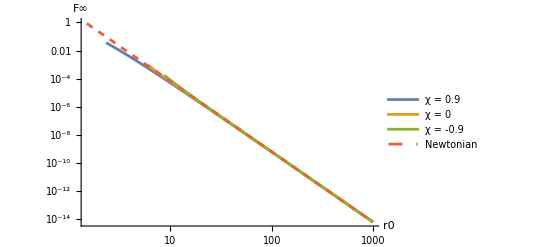

```mathematica
LogLogPlot[Evaluate[Append[Table[FluxInfMine[r0, chi], {chi, {0.9, 0., -0.9}}], 32/5 r0^-5]], {r0, 1.5, 1000}, PlotLegends -> {"χ = 0.9", "χ = 0", "χ = -0.9", "Newtonian"}, PlotStyle -> {Automatic, Automatic, Automatic, Dashed}, AxesLabel -> {"r0", "F∞"}]
```

(Each curve starts at its own ISCO; for r0 below it the map gives rC > 1 and the function returns unevaluated, so nothing is drawn.)

### 7.6 Compare with the package

```mathematica
Get[FileNameJoin[{dir, "FluxInterpolation.wl"}]];
{Max@Abs[Cinf - FluxInterpolation`FluxChebCoeffs[[1]]], FluxInterpolation`FluxInf[10., 0.] - FluxInfMine[10., 0.]}
```

{6.66134×10^-16,4.06576×10^-20}

Same coefficients, same result. You have now rebuilt FluxInterpolation.wl.

### Exercise 6: a real off-grid accuracy test

Chebyshev–Gauss grids are nested under odd refinement: the nodes of T_6 are a subset of those of T_18 (take i = 3i' + 1), and those of T_9 are a subset of those of T_27 (j = 3j' + 1). (a) Prove this from the node formula. (b) Build the interpolant from the 6 × 9 subgrid only, evaluate it at all 18 × 27 nodes, and compare with the true values. Most of those nodes are "off-grid" for the coarse interpolant, so this is a genuine accuracy test. (c) Compare the error with the size of the last coefficients of the coarse interpolant. (d) Where in the (rC, χ) square is the error largest?

#### Solution

(a) cos((2(3i'+1)+1)π/(2·18)) = cos(3(2i'+1)π/36) = cos((2i'+1)π/12) = node[i', 6]; the same with 27 and 9.

```mathematica
Max@Abs[N@Table[node[3 i + 1, 18] - node[i, 6], {i, 0, 5}]]
```

```mathematica
sub = Finf[[3 Range[0, 5] + 2, 3 Range[0, 8] + 2]];  (* +1 for 1-based lists *)
Ccoarse = chebCoeffs2D[sub];
errGrid = Table[chebEval2D[Ccoarse, data[[i, j, 1]], data[[i, j, 2]]]/Finf[[i, j]] - 1, {i, nR}, {j, nA}];
Max@Abs[errGrid]
```

```mathematica
{Max@Abs@Ccoarse[[-1]], Max@Abs@Ccoarse[[All, -1]]}
```

```mathematica
MatrixPlot[Log10@Map[Max[Abs[#], 10^-8] &, errGrid, {2}], FrameLabel -> {"row i (rC; ISCO at top)", "column j (χ; +0.998 at left)"}, PlotLegends -> Automatic, PlotLabel -> "Log10 rel. error, 6x9 interpolant (nodes used: 1e-8 floor)"]
```

The relative error is large (tens of percent), much larger than the last coefficients (~1e-2) suggest. Find where:

```mathematica
{Position[Abs@errGrid, Max@Abs@errGrid], Max@Abs@errGrid[[All, 2 ;;]], Finf[[1, 1 ;; 4]], N@data[[1, 1 ;; 4, 2]]}
```

Almost all of it sits in the first column, χ = 0.998. That column is outside the outermost coarse node (χ = cos(π/18) ≈ 0.985), and between the two f∞ changes by a factor of 3. The reason is physical: the ISCO radius contains (1 - χ)^(1/3), which is not analytic at χ = 1. There is a branch point just beyond the edge of the interval, and (Section 5) singularities close to the interval spoil convergence. The coarse grid never sees the steep region, so its coefficients cannot warn you about it.

Two lessons. (1) The coefficient tail is a good error estimate only once the grid resolves the function; nested subgrid tests like this one are the safer check. (2) This is exactly why Honet+ replace χ by a logarithmic variable in log(1 - χ) (eq. A12): it stretches the region near χ = 1 so the function becomes smooth in the new variable. The full 18 × 27 interpolant is far better than this 6 × 9 one, but its accuracy near χ = 0.998 is the least certain part of the grid.

### Exercise 7

Write fHorMine's physical counterpart FluxHorMine[r0, χ] = f_H/r0^(15/2), check it against FluxInterpolationFluxHor, and plot it versus r0 for χ = 0.9 and χ = -0.9. Why does it change sign for χ = 0.9? (Hint: superradiance, Ω < Ω_H.)

#### Solution

```mathematica
FluxHorMine[r0_?NumericQ, chi_?NumericQ] := fHorMine[2 rISCOmine[chi]/r0 - 1, chi]/r0^(15/2);
FluxHorMine[10., 0.9] - FluxInterpolation`FluxHor[10., 0.9]
```

```mathematica
Plot[{FluxHorMine[r0, 0.9], FluxHorMine[r0, -0.9]}, {r0, 2, 20}, PlotRange -> All, PlotLegends -> {"χ = 0.9", "χ = -0.9"}, AxesLabel -> {"r0", "F_H"}]
```

For prograde orbits the orbital frequency is below the horizon frequency (mΩ < mΩ_H), and the horizon flux is negative: superradiance extracts energy from the black hole and feeds it into the orbit.

## Summary

Nodes: x_i = cos((2i+1)π/(2n)), the roots of T_n (node in FluxGrid_nonspinning.nb).

Coefficients: a discrete cosine transform of the data, c = M·f in 1D and C = M_R·F·M_Aᵀ in 2D (chebCoeffs in the package).

Evaluation: p(x,y) = T(x)·C·T(y) with T_k(x) = cos(k arccos x) (chebT and chebEval in the package).

Accuracy: read it from the decay of the last coefficients, or test it with a nested subgrid.

Physics: compactify r0 to rC = 2r_*/r0 - 1, and interpolate r0^5 F_∞ and r0^(15/2) F_H, which are smooth and of order one, instead of the raw fluxes.